# refresh[ ]

## 計算例

```mathematica
Manipulate[
Refresh[Random[],UpdateInterval->If[go,0.105,Infinity]],
{{go,False},{True, False}}]
```

```mathematica
Refreshによって，Random[]が更新される
UpdateIntervalによって更新頻度が制御できる
```

```mathematica
x=1;
Manipulate[
Refresh[x=x+0.01;x,UpdateInterval->If[go,0.02,Infinity]],
{{go,False},{True, False}}]
```

```mathematica
これはUpdateIntervalがInfinityにもかかわらず暴走してしまう
そこでIfを挟んで代入を制御する
```

これはUpdateIntervalがInfinityにもかかわらず暴走してしまう

そこでIfを挟んで代入を制御する

```mathematica
x=1;
Manipulate[
Refresh[
If[go,x=x+0.01],UpdateInterval->If[go,1,Infinity]],
{{go,False},{True, False}}]
```

```mathematica
Manipulate[
Refresh[
If[go,x=x+0.01],UpdateInterval->If[go,0.502,Infinity]],
{{go,False},{True, False}},
Button["reset",go=False;x=100]
]
```

```mathematica
初期値をリセットボタンに割り当てる．xはグローバルに定義される
チェックボックスでonとoffは制御できるようになったが，UpdateIntervalは無視される
遅延割り当てにしてみたらどうか？
```

```mathematica
Manipulate[
Refresh[
If[go,x:=x+0.01],UpdateInterval->If[go,0.502,Infinity]],
{{go,False},{True, False}},
Button["reset",go=False;x=100]
]
```

```mathematica
うまくいかない
TrackedSymbols->{}でxを制御する
```

```mathematica
Manipulate[
Refresh[
If[go,x=x+0.01],TrackedSymbols:>{x},UpdateInterval->If[go,0.502,Infinity]],
{{go,False},{True, False}},
Button["reset",go=False;x=100]
]
```

```mathematica
TrackedSymbolsを使ってもうまくいかない
```

```mathematica
そもそもUpdateIntervalとはなにか？
UpdateIntervalはRefreshとDynamicのオプションで，更新する時間間隔を指定する．

はずなのだが．．．．
```

```mathematica
Dynamic[Refresh[DateString[],UpdateInterval->1]]
```

```mathematica
そもそも時間指定は「可能な場合に」，だから，指定通りにならない場合もある
```

```mathematica
Dynamic[Refresh[DateString[],UpdateInterval->0.01]]
```

```mathematica
オブジェクトの更新がそもそも1秒ごとなので，0.01を指定しても無視される
```

```mathematica
ProgressIndicator[Dynamic[y,UpdateInterval->0]]
```

```mathematica
y=0;While[y<1,y=y+10^-6]
```

```mathematica
オブジェクトを再帰的代入すると，refreshしてもうまくいかないらしい
次のような命令なら代入でも問題ないし，UpdateIntervalによる制御もうまくいく
```

```mathematica
Manipulate[
Refresh[
If[go,x=Random[]],UpdateInterval->If[go,0.8,Infinity]],
{{go,False},{True, False}},
Button["reset",go=False;x=100]
]
```

```mathematica
しかし再帰的に代入すると，Dynamicオブジェクトが自分自身を連続的に更新するので
UpdateIntervalを指定しても，機能しない（のではないかと推測する）
```

```mathematica
Manipulate[
Refresh[
If[go,x=x+Random[]],UpdateInterval->If[go,0.8,Infinity]],
{{go,False},{True, False}},
Button["reset",go=False;x=100]
]
```

## グラフィックオブジェクトの動的更新

```mathematica
次のコードは更新されない
```

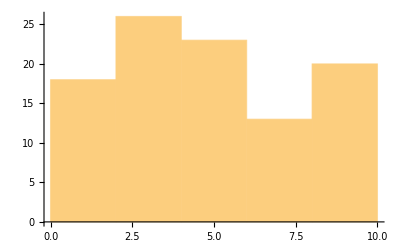

```mathematica
Refresh[Histogram[RandomReal[10,100]],UpdateInterval->0.1]
```

```mathematica
これなら更新される
```

```mathematica
Dynamic[Refresh[Histogram[RandomReal[10,100]],UpdateInterval->0.1]]
```

```mathematica
Manipulateのなかに入れると更新される.
スライダはダミー
```

```mathematica
Manipulate[Refresh[Histogram[RandomReal[10,100]],UpdateInterval->0.25],{x,0,1}]
```

```mathematica
上記の命令だと止まらないので，UpdateInterval　をIf文で制御する
チェックボックスxはデフォルトでFalse
If[x,0,Infinity]　により，　
チェック->UpdateInterval->0
チェックオフ->UpdateInterval->Infinity
```

```mathematica
Manipulate[Refresh[Histogram[RandomReal[10,1000]],UpdateInterval->If[x,0,Infinity]],{{x,False},{True, False}}]
```

```mathematica
複数のデータのヒストグラムはこうする
Histogram[{data1,data2,data3}]
```

```mathematica
Manipulate[Refresh[
Histogram[
{RandomVariate[NormalDistribution[0,1],500],RandomVariate[NormalDistribution[3,1/2],500]},PlotRange->{{-3,5},{0,200}}],
UpdateInterval->If[x,0,Infinity]],{{x,False},{True, False}}]
```

```mathematica
めっちゃ計算しているようにみえる,無意味なコード
```

```mathematica
Manipulate[Refresh[
Histogram[
{RandomVariate[NormalDistribution[0,1],n],
RandomVariate[NormalDistribution[a,1/2],n],
RandomVariate[NormalDistribution[10,1],n],
RandomVariate[LogNormalDistribution[1,0.3],n],
RandomVariate[NormalDistribution[8,0.5],n]},{.25},PlotRange->{{-3,15},{0,100}}],
UpdateInterval->If[x,0,Infinity]],
{{x,False,"Run MCMC"},{True, False}},
{{n,300},1,500,1},
{{a,3,"μ"},1,10}]
```

```mathematica
Manipulate[Refresh[Histogram[{RandomVariate[NormalDistribution[0,1],n],RandomVariate[NormalDistribution[a,1/2],n],RandomVariate[NormalDistribution[10,1],n],RandomVariate[LogNormalDistribution[1,0.3],n],RandomVariate[NormalDistribution[8,0.5],n]},{0.25},PlotRange->{{-3,15},{0,100}}],UpdateInterval->If[x,0,∞]],{{x,False,"Run MCMC"},{True,False}},{{n,300},1,500,1},{{a,3,"μ"},1,10}]
```

```mathematica
update関数を使ってplotを動的更新する
```

```mathematica
initialdata[n_]:={RandomVariate[NormalDistribution[0,1],n],RandomVariate[NormalDistribution[3,1/2],n]};
update[data_]:={
If[Length[data[[1]]]>0 ,Drop[data[[1]],1],{Null}],
If[Length[data[[2]]]>0,Drop[data[[2]],1],{Null}]};
(* update関数のほうに停止条件を書いておく. dataがなくなったらNullを返す*)
visualize[data_,hight_]:=Histogram[data,{1},PlotRange->{{-3,6},{0,hight}}];
(* histogram を遅延評価させるために,関数化する*)

sample=initialdata[50];
Manipulate[Refresh[
If[x,
sample=update[sample];visualize[sample,50]
],UpdateInterval->If[x,0.5,Infinity]],{{x,False},{True, False}}]
```

```mathematica
restartボタンの追加
Buttonで初期値をセットする．ただしButtonの実行文にvisualizeを入れてもplotは出てこない
(ボタンの位置がmanipulateの対象外だから？)
そこでvisualizeをif文から外に出し，Refresh内で自動的に初回だけ実行されるように変更する．
```

```mathematica
initialdata[n_]:={RandomVariate[NormalDistribution[0,1],n],RandomVariate[NormalDistribution[3,1/2],n]};
update[data_]:={
If[Length[data[[1]]]>0 ,Drop[data[[1]],1],{Null}],
If[Length[data[[2]]]>0,Drop[data[[2]],1],{Null}]};
(* update関数のほうに停止条件を書いておく. dataがなくなったらNullを返す*)
visualize[data_,hight_]:=Histogram[data,{1},PlotRange->{{-3,6},{0,hight}}];
(* histogram を遅延評価させるために,関数化する*)
sample=initialdata[50];


Manipulate[Refresh[
If[x,sample=update[sample]];
(* If文で実行する動作：UpdateInterval->0 のときだけ,update関数を再帰的代入する*)
visualize[sample,50],UpdateInterval->If[x,0.5,Infinity]],
{{x,False},{True, False}},
Button["restart",x=False;sample=initialdata[50];visualize[sample,50]]]
```

```mathematica
プロトタイプがうまくいったのでランチェスターの1次法則に組み入れる
```

```mathematica
initialdata[n_]:={RandomVariate[NormalDistribution[50,5],n],RandomVariate[NormalDistribution[49,5],n]};

fight[group_]:=Module[{id1,id2,n1,n2,power1,power2,winner1,winner2},
n1=Length[group[[1]]];n2=Length[group[[2]]];
id1=Range[n1];id2=Range[n2];(*初期兵ID*)
power1=group[[1]];power2=group[[2]];
winner1={};winner2={};
id1=RandomSample[id1];id2=RandomSample[id2];
Table[
If[(* 戦闘力を比較して勝者を残す*)
RandomChoice[
{power1⟦id1⟦i⟧⟧/(power1⟦id1⟦i⟧⟧+power2⟦id2⟦i⟧⟧),power2⟦id2⟦i⟧⟧/(power1⟦id1⟦i⟧⟧+power2⟦id2⟦i⟧⟧)}->{True,False}],
winner1=Append[winner1,power1⟦id1⟦i⟧⟧],
winner2=Append[winner2,power2⟦id2⟦i⟧⟧]
](* If end*),{i,1,Min[n1,n2]}](* Table end *);
{winner1,winner2}
];

(* update関数のほうに停止条件を書いておく. dataがなくなったらNullを返す*)
visualize[data_,hight_]:=Histogram[data,{1},PlotRange->{{0,100},{0,hight}}];
(* histogram を遅延評価させるために,関数化する*)

n=1000;ylim=100;
sample=initialdata[n];


Manipulate[Refresh[
If[x,sample=fight[sample]];
(* If文で実行する動作：UpdateInterval->0 のときだけ,update関数を再帰的代入する*)
visualize[sample,ylim],TrackedSymbols:>{},UpdateInterval->If[x,1,Infinity]],
{{x,False},{True, False}},
Button["restart",x=False;sample=initialdata[n];visualize[sample,ylim]]]
```

```mathematica
戦闘実行関数を改良する
1回の戦闘で1人だけ減る fightonce[ ];
```

```mathematica
initialdata[n_]:={RandomVariate[NormalDistribution[50,5],n],RandomVariate[NormalDistribution[49,5],n]};

fightonce[group_]:=Module[{power1,power2},
power1=group[[1]];power2=group[[2]];
If[Length[power1]>0&&Length[power2]>0,
power1=RandomSample[power1];
power2=RandomSample[power2];

If[(* 戦闘力を比較して勝者を残す*)
RandomChoice[
{power1⟦1⟧/(power1⟦1⟧+power2⟦1⟧),power2⟦1⟧/(power1⟦1⟧+power2⟦1⟧)}->{True,False}],
(* True -> 1が勝つ*)
power2=　Drop[power2,1],
power1=　Drop[power1,1]];(* If end*)
];(* If end*)
{power1,power2}
];

(* update関数のほうに停止条件を書いておく. dataがなくなったらNullを返す*)
visualize[data_,hight_]:=Histogram[data,{1},PlotRange->{{0,100},{0,hight}}];
(* histogram を遅延評価させるために,関数化する*)

n=50;ylim=25;
sample=initialdata[n];


Manipulate[Refresh[
If[x,sample=fightonce[sample]];
(* If文で実行する動作：UpdateInterval->0 のときだけ,update関数を再帰的代入する*)
visualize[sample,ylim],UpdateInterval->If[x,1,Infinity]],
{{x,False},{True, False}},
Button["restart",x=False;sample=initialdata[n];visualize[sample,ylim]]]
```

### fightonce[ ]

```mathematica
(* fightの引数は,{{集団1の兵力分布},{集団2の兵力分布}}  
というベクトル*)

initialdata[n_]:={RandomVariate[NormalDistribution[50,1],n],RandomVariate[NormalDistribution[49,1],n]};

fightonce[group_]:=Module[{power1,power2},
power1=group[[1]];power2=group[[2]];
If[Length[power1]>0&&Length[power2]>0,
power1=RandomSample[power1];
power2=RandomSample[power2];

If[(* 戦闘力を比較して勝者を残す*)
RandomChoice[
{power1⟦1⟧/(power1⟦1⟧+power2⟦1⟧),power2⟦1⟧/(power1⟦1⟧+power2⟦1⟧)}->{True,False}],
(* True -> 1が勝つ*)
power2=　Drop[power2,1],
power1=　Drop[power1,1]];(* If end*)
];(* If end*)
{power1,power2}
];
```

```mathematica
(* 動作確認 *)
```

```mathematica
x=initialdata[5];
Do[x=fightonce[x];Print[x],{10}]
```

{{50.7671,49.5617,50.7874,48.8333},{49.5046,50.8581,48.1384,49.9923,49.305}}

{{49.5617,48.8333,50.7874,50.7671},{49.305,50.8581,49.9923,49.5046}}

{{50.7671,50.7874,48.8333,49.5617},{50.8581,49.305,49.9923}}

{{50.7671,48.8333,50.7874},{50.8581,49.9923,49.305}}

{{50.7671,50.7874,48.8333},{50.8581,49.9923}}

{{50.7874,50.7671},{50.8581,49.9923}}

{{50.7671},{50.8581,49.9923}}

{{50.7671},{50.8581}}

{{},{50.8581}}

{{},{50.8581}}

```mathematica
fightonce[]を使ってManipulateを一般化する
平均，分散パラメータをスライダで指定
```

```mathematica
(* 関数の定義 *)
initialdata[n_,m1_,m2_]:={RandomVariate[NormalDistribution[m1,5],n],RandomVariate[NormalDistribution[m2,5],n]};

fightonce[group_]:=Module[{power1,power2},
power1=group[[1]];power2=group[[2]];
If[Length[power1]>0&&Length[power2]>0,
power1=RandomSample[power1];
power2=RandomSample[power2];

If[(* 戦闘力を比較して勝者を残す*)
RandomChoice[
{power1⟦1⟧/(power1⟦1⟧+power2⟦1⟧),power2⟦1⟧/(power1⟦1⟧+power2⟦1⟧)}->{True,False}],
(* True -> 1が勝つ*)
power2=　Drop[power2,1],
power1=　Drop[power1,1]];(* If end*)
];(* If end*)
{power1,power2}
];

(* update関数のほうに停止条件を書いておく. dataがなくなったらNullを返す*)
visualize[data_,hight_]:=Histogram[data,{1},PlotRange->{{0,100},{0,hight}}];
(* histogram を遅延評価させるために,関数化する*)

(*n=50;ylim=25;sample=initialdata[n];*)


Manipulate[Refresh[
If[x,sample=fightonce[sample]];
(* If文で実行する動作：UpdateInterval->0 のときだけ,update関数を再帰的代入する*)
visualize[sample,ylim],UpdateInterval->If[x,0,Infinity]],
{{x,False},{True, False}},
{{n,100},50,1000,1},{{m1,40},10,70},{{m2,50},10,70},
Button["reset",x=False;sample=initialdata[n,m1,m2];ylim=n/5]]
```

```mathematica
initialdata[n_]:={RandomVariate[NormalDistribution[0,1],n],RandomVariate[NormalDistribution[3,1/2],n]};
update[data_]:={
If[Length[data[[1]]]>0 ,Drop[data[[1]],1],{Null}],
If[Length[data[[2]]]>0,Drop[data[[2]],1],{Null}]};
(* update関数のほうに停止条件を書いておく. dataがなくなったらNullを返す*)
visualize[data_,hight_]:=Histogram[data,{1},PlotRange->{{-3,6},{0,hight}}];
(* histogram を遅延評価させるために,関数化する*)
sample=initialdata[50];


Manipulate[Refresh[
If[x,
sample=update[sample];visualize[sample,50]
],UpdateInterval->If[x,0.5,Infinity]],
{{x,False},{True, False}},
Button["restart",x=False;sample=initialdata[50];visualize[sample,50]]]
```

```mathematica
n=5;
initialdata[n_]:={RandomVariate[NormalDistribution[0,1],n],RandomVariate[NormalDistribution[3,1/2],n]};
update[data_]:={Drop[data[[1]],1],Drop[data[[2]]],1};
visualize[data_]:=Histogram[data];
(* histogram を遅延評価させるために,関数化する*)
```

{{-1.61201,1.3486,-0.35738,-0.742277,-0.311383},{3.13643,3.37303,3.6597,2.50622,3.21077}}

{{1.3486,-0.35738,-0.742277,-0.311383},{3.13643,3.37303,3.6597,2.50622,3.21077},1}

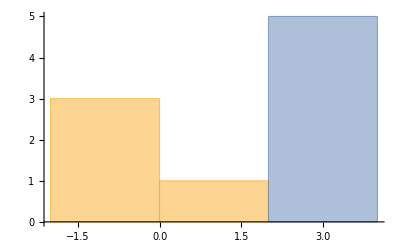

{{-0.35738,-0.742277,-0.311383},{3.13643,3.37303,3.6597,2.50622,3.21077},1}

```mathematica
sample=initialdata[];
sample
sample=update[sample];
sample
visualize[sample]
sample=update[sample];
sample
```

```mathematica
initialdata[n_]:={RandomVariate[NormalDistribution[0,1],n],RandomVariate[NormalDistribution[3,1/2],n]};
update[data_]:=
If[Length[data[[1]]]>0 && Length[data[[2]]]>0,
{Drop[data[[1]],1],Drop[data[[2]],1]},{0,0}];
(* update関数のほうに停止条件を書いておく*)
visualize[data_,hight_]:=Histogram[data,{1},PlotRange->{0,hight}];


sample=initialdata[50];
Manipulate[Refresh[
If[x,
sample=update[sample];visualize[sample,50]
],UpdateInterval->If[x,0.1,Infinity]],{{x,False},{True, False}}]
```

```mathematica
sample=initialdata[20];
Manipulate[Refresh[
If[x,
sample1=update[sample];;sample=sample1
],UpdateInterval->If[x,0,Infinity]],{{x,False},{True, False}}]
```

## 以下はゴミ

```mathematica
initialset[n01_,n02_]:={RandomReal[10,n01],RandomReal[10,n02]};
fight[group_]:={Drop[group[[1]],1],Drop[group[[2]],1]};

Manipulate[
Refresh[
If[oldn1≠n1||oldn2≠n2,x=initialset[n1,n2];moving=False;oldn1=n1;oldn2=n2;state=Text[Style["END !",Red,20]]
];

If[moving,x=fight[x];
state1=Length[x[[1]]];
state2=Length[x[[2]]];
ListPlot[{{{1,state1}},{{2,state2}}},Filling->Axis,PlotRange->{{0,3},{0,Max[state1,state2]+1}},PlotMarkers->{"group1","group2"}]],
UpdateInterval->If[moving,0.2,Infinity]
](* reflesh end *),
(*  人数だけを 監視して，全滅したらmoving をFalseに切り替え,Dynamic[state]表示をendに変える．
moving の値がFalseになると　{group1,group2}の更新が終わり，"run simulation"チェックボックスがoffになる*)
{{n1,50,"number of group1"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
{{n2,50,"number of group2"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
{{oldn1,50},ControlType->None},(*初期値だけoldn1,oldn2で設定  *)
{{oldn2,50},ControlType->None},

{{moving,False,"run simulation"},{True, False}},
Button["reset",moving=False;state="going...";
x=initialset[n1,n2];
state1=Length[x[[1]]];state2=Length[x[[2]]];ListPlot[{{{1,state1}},{{2,state2}}},Filling->Axis,PlotRange->{{0,3},{0,Max[state1,state2]+1}},PlotMarkers->{"group1","group2"}],
ImageSize->Medium],
Dynamic[{"state=",state}],SaveDefinitions->True,TrackedSymbols->{state1,state2,x},SynchronousUpdating->True,ControlPlacement->Left
]
```

```mathematica
ver000
```

```mathematica
initialset[n1_,n2_]:={RandomReal[10,n1],RandomReal[10,n2]};
fight[group_]:={Drop[group[[1]],1],Drop[group[[2]],1]};

Manipulate[
Dynamic[Refresh[
If[moving,{group1,group2}=fight[{group1,group2}]](* 更新している部分 *);
If[(Length[group1]==0)||(Length[group2]==0),(* どちらか0人になったら止める *)
(*停止条件を満たした場合のplot*)
ListPlot[{{{1,group1}},{{2,group2}}},Filling->Axis,PlotRange->{{0,3},{0,Max[group2n,group1n]+1}},PlotMarkers->{"group1","group2"}];
moving=False;state=Text[Style["END !",Red,20]],
moving=moving;state1=Length[group1]//N;state2=Length[group2]//N;
ListPlot[{{{1,state1}},{{2,state2}}},Filling->Axis,PlotRange->{{0,3},{0,Max[group2n,group1n]+1}},PlotMarkers->{"group1","group2"}]
],TrackedSymbols->{},UpdateInterval->If[moving,1,Infinity]](* reflesh end *)](*dynamic end*),
(*  人数だけを 監視して，全滅したらmoving をFalseに切り替え,Dynamic[state]表示をendに変える．
moving の値がFalseになると　{group1,group2}の更新が終わり，"run simulation"チェックボックスがoffになる*)
{{group1n,50,"number of group1"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
{{group2n,50,"number of group2"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
{{moving,False,"run simulation"},{True, False}},
Button["reset",moving=False;state="going...";x=initialset[group1n,group2n];group1=x[[1]];group2=x[[2]],
ImageSize->Medium],
Dynamic[{"state=",state}],SaveDefinitions->True,TrackedSymbols->{},SynchronousUpdating->True,ControlPlacement->Left
]
```

```mathematica
x=.
```

```mathematica
x
```

x

```mathematica
Manipulate[Dynamic[Refresh[c=c,TrackedSymbols:>{c},UpdateInterval->5]],{c,0,5,1}]
```

```mathematica
Module[{x},{Slider[Dynamic[x]],Dynamic[x]}]
```

{,}

```mathematica
initialset[n1_,n2_]:={RandomReal[10,n1],RandomReal[10,n2]};
fight[group_]:={Drop[group[[1]],1],Drop[group[[2]],1]};

Manipulate[
Dynamic[
Refresh[
If[(Length[group1]≥1)&&(Length[group2]≥1),(*停止条件 *)
{group1,group2}=fight[{group1,group2}];ListPlot[{{{1,state1}},{{2,state2}}},Filling->Axis,PlotRange->{{0,3},{0,Max[group2n,group1n]+1}},PlotMarkers->{"group1","group2"}],
(* 停止条件を満たした場合の処理 *)
moving=False;state=Text[Style["END !",Red,20]]
],TrackedSymbols->{},UpdateInterval->If[moving,0.2,Infinity]
](* reflesh end *)](*dynamic end*),
(*  人数だけを 監視して，全滅したらmoving をFalseに切り替え,Dynamic[state]表示をendに変える．
moving の値がFalseになると　{group1,group2}の更新が終わり，"run simulation"チェックボックスがoffになる*)
{{group1n,50,"number of group1"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
{{group2n,50,"number of group2"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
{{moving,False,"run simulation"},{True, False}},
Button["reset",moving=False;state="going...";x=initialset[group1n,group2n];group1=x[[1]];group2=x[[2]],
ImageSize->Medium],
Dynamic[{"state=",state}],SaveDefinitions->True,TrackedSymbols->{},SynchronousUpdating->True,ControlPlacement->Left
]
```

```mathematica
initialset[n1_,n2_]:={RandomReal[10,n1],RandomReal[10,n2]};
fight[group_]:={Drop[group[[1]],1],Drop[group[[2]],1]};

Manipulate[
Dynamic[
While[(Length[group[[1]]]≥1)&&(Length[group[[2]]]≥1),group=fight[group];
ListPlot[{{{1,state1}},{{2,state2}}},Filling->Axis,PlotRange->{{0,3},{0,Max[group2n,group1n]+1}},PlotMarkers->{"group1","group2"}]]],
(*  人数だけを 監視して，全滅したらmoving をFalseに切り替え,Dynamic[state]表示をendに変える．
moving の値がFalseになると　{group1,group2}の更新が終わり，"run simulation"チェックボックスがoffになる*)
{{group1n,50,"number of group1"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
{{group2n,50,"number of group2"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
Button["reset",group=initialset[group1n,group2n],ImageSize->Medium],
SaveDefinitions->True,TrackedSymbols->{},SynchronousUpdating->True,ControlPlacement->Left
]
```

```mathematica
initialset[n1_,n2_]:={RandomReal[10,n1],RandomReal[10,n2]};
fight[group_]:={Drop[group[[1]],1],Drop[group[[2]],1]};

group=initialset[50,50];

Manipulate[
Refresh[
While[(Length[group1]≥1)&&(Length[group2]≥1),
{group1,group2}=fight[{group1,group2}];
ListPlot[{{{1,state1}},{{2,state2}}},Filling->Axis,PlotRange->{{0,3},{0,Max[group2n,group1n]+1}},PlotMarkers->{"group1","group2"}]],UpdateInterval->1],
(*  人数だけを 監視して，全滅したらmoving をFalseに切り替え,Dynamic[state]表示をendに変える．
moving の値がFalseになると　{group1,group2}の更新が終わり，"run simulation"チェックボックスがoffになる*)
{{n1,50,"number of group1"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
{{n2,50,"number of group2"},1,100,1,ImageSize->Tiny,Appearance->"Labeled"},
SaveDefinitions->True,TrackedSymbols->{},SynchronousUpdating->True,ControlPlacement->Left
]
```

```mathematica
{group1,group2}=initialset[50,50];
```

```mathematica
group1
```

{}

```mathematica
group
```

{{7.7427,4.11349,4.58249,2.947,5.26614,0.563289,7.73069,7.28658,2.80986,3.69701,5.97205,6.28756,8.70096,0.860754,1.01758,5.07792,2.27055,2.93356,8.23959,4.7291,8.2077,2.23905,6.52815,4.55572,8.60859,3.81144,8.75809,6.65128,5.27645,1.43005,7.83466,6.17657,6.23786,8.16169,3.83211,3.89493,3.44631,7.55063,7.25218,8.08281,6.46682,5.4416,3.89876,5.89279,8.30979,2.60673,7.37924,3.29732,2.93093,1.8928},{6.47848,2.25931,2.82713,5.47048,4.81445,2.55318,4.25039,0.279118,5.38632,1.41484,6.29459,9.31046,7.48152,7.26926,4.00983,1.87233,4.05978,2.42613,2.18148,1.91232,9.08374,6.28735,3.06936,1.64945,4.54688,8.59741,1.59891,4.41547,9.61527,7.40126,9.89716,5.02722,1.56223,4.54523,9.24856,1.37809,4.42509,4.22183,9.99181,8.33459,6.99464,6.7442,1.8101,3.37731,7.55067,3.10877,4.16965,4.10151,8.42307,8.8163}}